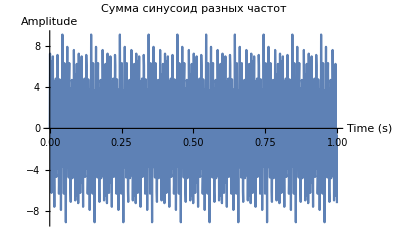

```mathematica
amplitude1=5;
frequencyHz1=300;

amplitude2=3;
frequencyHz2=120;

amplitude3=1.5;
frequencyHz3=50;

durationSec=1;
sampleRate=1000;

t=Range[0,durationSec-1/sampleRate,1/sampleRate];

(*Сумма синусоидальных компонент*)
dataPoints=amplitude1*Sin[2*Pi*frequencyHz1*t]+amplitude2*Sin[2*Pi*frequencyHz2*t]+amplitude3*Sin[2*Pi*frequencyHz3*t];

n=Length[dataPoints];

(*Построение временного сигнала*)
ListLinePlot[Transpose[{t,dataPoints}],PlotRange->All,AxesLabel->{"Time (s)","Amplitude"},PlotLabel->"Сумма синусоид разных частот"]
```

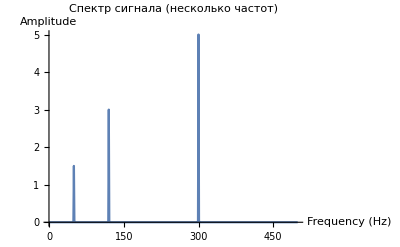

```mathematica
(*Выполнение ДПФ*)fourier=Fourier[dataPoints,FourierParameters->{1,-1}];

(*Частотная сетка*)
freqs=Range[0,n-1]*(sampleRate/n);

(*Масштаб амплитуд*)
scaledAmplitude=2*Abs[fourier]/n;

(*Первая половина спектра*)
halfLength=Floor[n/2];
freqsHalf=Take[freqs,halfLength];
amplitudeHalf=Take[scaledAmplitude,halfLength];

(*Построение спектра*)
ListLinePlot[Transpose[{freqsHalf,amplitudeHalf}],PlotRange->All,AxesLabel->{"Frequency (Hz)","Amplitude"},PlotLabel->"Спектр сигнала (несколько частот)"]
```